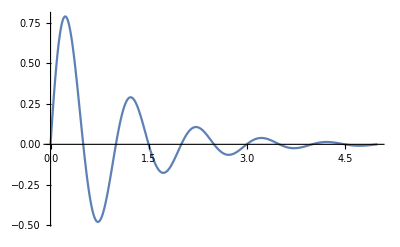

```mathematica
plt = Plot[ⅇ^-x Sin[2π x],{x,0,5},PlotRange->Full]
```

```mathematica
fname = "sampleplot_"<>ToString@Floor[SessionTime[]]<>".png";
Export[plt,fname];
SendMail[SendMail[
"To"->"huft@wisc.edu",
"Subject"->"MathMail",
"Body"->{"Here chap, have a plot: ",plt}
]
]
```

Export::chtype: First argument … is not a valid file specification.

CloudConnect::creds: Incorrect username or password.

CloudConnect::notauth: Unable to authenticate with Wolfram Cloud server. Please try authenticating again.

Part::partd: Part specification $Failed⟦1,0⟧ is longer than depth of object.

Part::partd: Part specification $Canceled⟦1,0⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Canceled